# Full Hamiltonian of TlF BΠ State

## by Eric Norrgard

Matrices are ordered J,Ω,F1,F.
Full States are S,J,Ω,I1,F1,I2,F

```mathematica
ClearAll["Global`*"]
Isotope=205;

I1=1/2; (*Tl nuclear spin*)
I2=1/2;(*F nuclear spin*)
S=1; (*Total electron spin*)
v=0;(*Excited state vibrational quantum number*)
	
μN205=+1.63821461 (*Nuclear magnetic moment of^205 Tl, nuclear magnetons*)
m203=202.97234422; (*mass 203Tl, amu*)
m205=204.974427541; (*mass 205Tl,amu *)
m19=18.998403224; (*mass 19F, amu *)
μ203=(m203*m19)/(m203+m19); (*reduced mass 203TlF *)
μ205=(m205*m19)/(m205+m19); (*reduced mass 205TlF *)
MassRatio = Piecewise[{{1, Isotope==205}, {μ205/μ203, Isotope==203}, {0, True}}];


Yground[l_,m_]:=29979.2458 Piecewise[{{476.942, l==1&&m==0}, {-2.2352, l==2&&m==0}, {0.223150144, l==0&&m==1}, {-1.503799*10^-3, l==1&&m==1}, {3.120*10^-6, l==2&&m==1}, {4.0*10^-9, l==3&&m==1}, {-1.95402*10^-7, l==0&&m==2}, {8.3*10^-11, l==1&&m==2}, {-6.853*10^-14, l==0&&m==3}, {0, True}}]
Y[l_,m_]:=29979.2458 Piecewise[{{367.21, l==1&&m==0}, {-9.985, l==2&&m==0}, {-1.350, l==3&&m==0}, {0.2261792, l==0&&m==1}, {-6.609*10^-3, l==1&&m==1}, {1.134*10^-3, l==2&&m==1}, {-3.359*10^-4, l==3&&m==1}, {-4.278*10^-7, l==0&&m==2}, {1.757*10^-7, l==1&&m==2}, {-9.19*10^-8, l==2&&m==2}, {1.07*10^-12, l==0&&m==3}, {-8.12*10^-12, l==1&&m==3}, {0, True}}]
(*Dunham Coefficients for TlF B state from Tiemann, Molecular Physics, Vol 65, No. 2, 359-375 (1988). *)
q[l_,m_]:=29979.2458 Piecewise[{{9.59*10^-5, l==0&&m==1}, {-2.81*10^-4, l==1&&m==1}, {1.79*10^-4, l==2&&m==1}, {-3.74*10^-5, l==3&&m==1}, {-2.71*10^-9, l==0&&m==2}, {0, True}}]


DunhamSum=Table[Sum[MassRatio^((l+2m)/2)*Y[l,m]*(v+1/2)^l*(J(J+1))^m,{l,0,3},{m,1,3}],{J,1,75}]; 
DunhamSumf=Table[Sum[MassRatio^((l+2m)/2)*q[l,m]*(v+1/2)^l*(J(J+1))^m,{l,0,3},{m,1,2}],{J,1,75}];
 
DunhamSumGround=Table[Sum[MassRatio^((l+2m)/2)*Yground[l,m]*(v+1/2)^l*(J(J+1))^m,{l,0,3},{m,1,3}],{J,0,75}]; 
DunhamSumGroundNoJ0=Table[Sum[MassRatio^((l+2m)/2)*Yground[l,m]*(v+1/2)^l*(J(J+1))^m,{l,0,3},{m,1,3}],{J,1,75}]; 

(*Calculate the first 50 diagonal matrix elements to save time in the calculation.  For state with J'=J, use DunhamSum[[J]].
Ignores m=0 terms, which are only due to vibration and just form an over all offset. *)
Rbranch=Flatten[Import["TlF R Branch Energies.xlsx"]];
Qbranch=Flatten[Import["TlF Q Branch Energies.xlsx"]];
UV=Flatten[ Table[{DunhamSumGround[[i+1]]+Rbranch[[1+4*i]],DunhamSumGround[[i+1]]+Rbranch[[2+4*i]],DunhamSumGround[[i+1]]+Rbranch[[3+4*i]],DunhamSumGround[[i+1]]+Rbranch[[4+4*i]]},{i,0,Length[Rbranch]/4-1}]];
UVQ=Flatten[Join[ Table[{DunhamSumGround[[i+1]]+Qbranch[[1+4*i-4]],DunhamSumGround[[i+1]]+Qbranch[[2+4*i-4]],DunhamSumGround[[i+1]]+Qbranch[[3+4*i-4]],DunhamSumGround[[i+1]]+Qbranch[[4+4*i-4]]},{i,1,Length[Qbranch]/4}],Table[{DunhamSumGround[[i+1]]+Qbranch[[1+4*i-4]],DunhamSumGround[[i+1]]+Qbranch[[2+4*i-4]],DunhamSumGround[[i+1]]+Qbranch[[3+4*i-4]]},{i,(Length[Qbranch]+1)/4,(Length[Qbranch]+1)/4}]]];
UVCOM=Mean[Table[UV[[j]],{j,1,4}]];

splittings=Piecewise[{{Flatten[Import["203TlF splittings - weighted.xlsx"],1][[;;,1]], Isotope==203}, {Flatten[Import["205TlF splittings - weighted.xlsx"],1][[;;,1]], Isotope==205}}];

weights=Piecewise[{{Flatten[Import["203TlF splittings - weighted.xlsx"],1][[;;,2]], Isotope==203}, {Flatten[Import["205TlF splittings - weighted.xlsx"],1][[;;,2]], Isotope==205}}];

(*highsplittings=Flatten[Import["205TlF high b Q splittings.xlsx"]];*)
(*DeletedSplittings={{43},{44},{45}} ;205TlF splittings Q 1 to 17.xlsx removed these cases when comparing measured and calculated splittings because no data are available at these postitions*)
maxf=Piecewise[{{9, Isotope==203}, {22, Isotope==205}}];
fvaluesforQbranch=Table[j,{j,2,maxf}];
DeletedSplittings=Piecewise[{{{{25},{26},{27}}, Isotope==203}, {Join[Table[{i},{i,28,30}],Table[{i},{i,34,45}],Table[{i},{i,49,60}],Table[{i},{i,64,66}]], Isotope==205}}];

MagneticHF1[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:= Ω*KroneckerDelta[0,F1-F1p,F-Fp](-1)^(J+Jp+I1+F1-Ω)SixJSymbol[{I1,J,F1p},{Jp,I1,1}]*ThreeJSymbol[{J,-Ω},{1,0},{Jp,Ωp}]√((2Jp+1)(2J+1)I1(I1+1)(2I1+1))

MagneticHF2[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:= Ω*KroneckerDelta[0,F-Fp](-1)^(2*F1p+I1+I2+F+1+2*J-Ω)SixJSymbol[{I2,F1,Fp},{F1p,I2,1}]SixJSymbol[{I1,J,F1},{1,F1p,Jp}]*ThreeJSymbol[{J,-Ω},{1,0},{Jp,Ωp}]√((2F1p+1)(2F1+1)(2Jp+1)(2J+1)I2(I2+1)(2I2+1))

NuclearSpinRotation1[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:= KroneckerDelta[0,F1-F1p,J-Jp,F-Fp,Ω-Ωp]*(J/2*KroneckerDelta[0,F1p-J-1/2]-(J+1)/2*KroneckerDelta[0,F1p-J+1/2])

NuclearSpinRotation2[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:= KroneckerDelta[0,J-Jp,F-Fp,Ω-Ωp](-1)^(2F1p+F+J+I1+I2+1)*(J/2*KroneckerDelta[0,F1-J-1/2,F-1-J]-(J+1)/2*KroneckerDelta[0,F1-J+1/2,F+1-J]+(-1)^(1+ F1p+J)   √((1+2 F1p) (1+2 (-1/2+J)) J (1+J) (1+2 J)((-3-2 F1p+2 J) (-1+2 F1p+2 J))/(2J (1+2 J)))/4*KroneckerDelta[0,F1-J+1/2,F-J]+
(-1)^(F1p+ J)   √(-((3-2 F1p+2 J) (5+2 F1p+2 J))/(2(1+J) (1+2 J))(1+2 F1p) J (1+J) (1+2 J) (1+2 (1/2+J)))/4*KroneckerDelta[0,F1-J-1/2,F-J])

(*p[J_,Ω_,F1_,F_,Jp_,Ωp_,F1p_,Fp_]:=(-1)^(J-S);*)

(*Rotation[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(BrotExcited*J(J+1)+DExcited*J^2(J+1)^2)*KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]*)

(*Dunham[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=B*J(J+1)*KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]
*)
Dunham[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=DunhamSum[[J]]*KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]

RotationB[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=J*(J+1)KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]
RotationD[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(J*(J+1))^2*KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]
RotationH[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(J*(J+1))^3*KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]



(*StarkExcited[J_,Ω_,F1_,F_,Jp_,Ωp_,F1p_,Fp_]:=-ℰ*dB*(-1)^(F+Fp+F1+F1p+2J+I1+I2-mF-Ω)((2F+1)(2Fp+1)(2F1+1)(2F1p+1)(2J+1)(2Jp+1))^(1/2)*ThreeJSymbol[{F,-mF},{1,0},{Fp,mF}]ThreeJSymbol[{J,-Ω},{1,0},{Jp,Ωp}]SixJSymbol[{F1p,Fp,I2},{F,F1,1}]SixJSymbol[{Jp,F1p,I1},{F1,J,1}]*)






MagneticHF1P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=
(MagneticHF1[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+
(-1)^(J-S+KroneckerDelta[0,P+1])MagneticHF1[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+
(-1)^(Jp-S+KroneckerDelta[0,Pp+1])MagneticHF1[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+
(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])MagneticHF1[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

MagneticHFq1P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(-1)^(J-S+KroneckerDelta[0,Pp+1])MagneticHF1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]/2

MagneticHFD1P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(J(J+1)+Jp(Jp+1))/2 MagneticHF1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]

MagneticHF2P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=
(MagneticHF2[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+
(-1)^(J-S+KroneckerDelta[0,P+1])MagneticHF2[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+
(-1)^(Jp-S+KroneckerDelta[0,Pp+1])MagneticHF2[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+
(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])MagneticHF2[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

MagneticHFq2P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(-1)^(J-S+KroneckerDelta[0,Pp+1])MagneticHF2P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]/2

NuclearSpinRotation1P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(NuclearSpinRotation1[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])NuclearSpinRotation1[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])NuclearSpinRotation1[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])NuclearSpinRotation1[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

NuclearSpinRotationq1P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(-1)^(J-S+KroneckerDelta[0,Pp+1])NuclearSpinRotation1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]/2


NuclearSpinRotation2P[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(NuclearSpinRotation2[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])NuclearSpinRotation2[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])NuclearSpinRotation2[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])NuclearSpinRotation2[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

RotationBP[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(RotationB[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])RotationB[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])RotationB[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])RotationB[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

RotationDP[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(RotationD[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])RotationD[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])RotationD[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])RotationD[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

RotationHP[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(RotationH[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])RotationH[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])RotationH[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])RotationH[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2

DunhamP[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(Dunham[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])Dunham[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])Dunham[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])Dunham[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2+KroneckerDelta[0,J-Jp,Ω-Ωp,F1-F1p,F-Fp,P-Pp]*(-1)^(J-S+KroneckerDelta[0,Pp+1])DunhamSumf[[J]]/2

(*LambdaDoublingP[J_,Ω_,F1_,F_,P_,Jp_,Ωp_,F1p_,Fp_,Pp_]:=(LambdaDoubling[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(J-S+KroneckerDelta[0,P+1])LambdaDoubling[J,-Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]+(-1)^(Jp-S+KroneckerDelta[0,Pp+1])LambdaDoubling[J,Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp]+(-1)^(J+Jp-2S+KroneckerDelta[0,P+1]+KroneckerDelta[0,Pp+1])LambdaDoubling[J,-Ω,F1,F,P,Jp,-Ωp,F1p,Fp,Pp])/2*)

MHF1Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
MagneticHF1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
MHFq1Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
MagneticHFq1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
MHFD1Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
MagneticHFD1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
MHF2Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
MagneticHF2P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
MHFq2Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
MagneticHFq2P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
NSR1Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
NuclearSpinRotation1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
NSRq1Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
NuclearSpinRotationq1P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
NSR2Pcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
NuclearSpinRotation2P[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
DPcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
DunhamP[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
RotBPcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
RotationBP[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
RotDPcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
RotationDP[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]
RotHPcomp=Compile[{J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp},
RotationHP[J,Ω,F1,F,P,Jp,Ωp,F1p,Fp,Pp]]


(*
\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\////////////////////////////////////////
Select the parts of the Hamiltonian you would like by un-commenting them out.  Do this in all 3 sections, i.e. hamiltonian, hamiltonian0, and hamiltonian1.  hamiltonian0 and hamiltonian1 are special cases of hamiltonian where F=0,1.
///////////////////////////////\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\
*)

hamiltonian[x_,y_]:=(*DPcomp@@rrr[[x,y]]*)Be*RotBPcomp@@rrr[[x,y]]-De*RotDPcomp@@rrr[[x,y]]+He*RotHPcomp@@rrr[[x,y]]+ h1*MHF1Pcomp@@rrr[[x,y]](*+hq1*MHFq1Pcomp@@rrr[[x,y]]*)(*+h1D*MHFD1Pcomp@@rrr[[x,y]]*)+h2*MHF2Pcomp@@rrr[[x,y]]+(*hq2*MHFq2Pcomp@@rrr[[x,y]]+*)cI1*NSR1Pcomp@@rrr[[x,y]]+(*cI1q*NSRq1Pcomp@@rrr[[x,y]]+*)cI2*NSR2Pcomp@@rrr[[x,y]]
hamiltonian0[x_,y_]:=(*DPcomp@@rrr0[[x,y]]*)Be*RotBPcomp@@rrr0[[x,y]]-De*RotDPcomp@@rrr0[[x,y]]+He*RotHPcomp@@rrr0[[x,y]]+ h1*MHF1Pcomp@@rrr0[[x,y]](*+hq1*MHFq1Pcomp@@rrr0[[x,y]]*)(*+h1D*MHFD1Pcomp@@rrr0[[x,y]]*)+h2*MHF2Pcomp@@rrr0[[x,y]]+(*hq2*MHFq2Pcomp@@rrr0[[x,y]]+*)cI1*NSR1Pcomp@@rrr0[[x,y]]+(*cI1q*NSRq1Pcomp@@rrr0[[x,y]]+*)cI2*NSR2Pcomp@@rrr0[[x,y]]
hamiltonian1[x_,y_]:=(*DPcomp@@rrr1[[x,y]]*)Be*RotBPcomp@@rrr1[[x,y]]-De*RotDPcomp@@rrr1[[x,y]]+He*RotHPcomp@@rrr1[[x,y]]+ h1*MHF1Pcomp@@rrr1[[x,y]](*+hq1*MHFq1Pcomp@@rrr1[[x,y]]*)(*+h1D*MHFD1Pcomp@@rrr1[[x,y]]*)+h2*MHF2Pcomp@@rrr1[[x,y]]+(*hq2*MHFq2Pcomp@@rrr1[[x,y]]+*)cI1*NSR1Pcomp@@rrr1[[x,y]]+(*cI1q*NSRq1Pcomp@@rrr1[[x,y]]+*)cI2*NSR2Pcomp@@rrr1[[x,y]]

states={{F-1,1,F-I1,F,1},
{F,1,F-I1,F,1},
{F,1,F+I1,F,1},
{F+1,1,F+I1,F,1},
{F-1,1,F-I1,F,-1},
{F,1,F-I1,F,-1},
{F,1,F+I1,F,-1},
{F+1,1,F+I1,F,-1}};
statesF0={{1,1,1/2,0,1},
{1,1,1/2,0,-1}};
statesF1={{1,1,1/2,1,1},
{1,1,3/2,1,1},
{2,1,3/2,1,1},
{1,1,1/2,1,-1},
{1,1,3/2,1,-1},
{2,1,3/2,1,-1}};
rrr=Outer[Join,states,states,1];
rrr0=Outer[Join,statesF0,statesF0,1];
rrr1=Outer[Join,statesF1,statesF1,1];

(*Quiet[fullhamiltonian=Outer[hamiltonian,Table[i,{i,Length[states],1,-1}],Table[i,{i,Length[states],1,-1}]]];
Quiet[fullhamiltonian0=Outer[hamiltonian0,Table[i,{i,Length[statesF0],1,-1}],Table[i,{i,Length[statesF0],1,-1}]]];
Quiet[fullhamiltonian1=Outer[hamiltonian1,Table[i,{i,Length[statesF1],1,-1}],Table[i,{i,Length[statesF1],1,-1}]]];*)

Quiet[fullhamiltonian=Outer[hamiltonian,Table[i,{i,1,Length[states],1}],Table[i,{i,1,Length[states],1}]]];
Quiet[fullhamiltonian0=Outer[hamiltonian0,Table[i,{i,1,Length[statesF0],1}],Table[i,{i,1,Length[statesF0],1}]]];
Quiet[fullhamiltonian1=Outer[hamiltonian1,Table[i,{i,1,Length[statesF1],1}],Table[i,{i,1,Length[statesF1],1}]]];
```

1.63821

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Part::pkspec1: The expression 3/2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

Part::partd: Part specification Flatten[$Failed,1]⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

Part::partd: Part specification Flatten[$Failed,1]⟦1;;All,2⟧ is longer than depth of object.

CompiledFunction[…]

CompiledFunction[…]

CompiledFunction[…]

«9 more identical outputs»

```mathematica
(*Set the spectroscopic constants here.  These are for the f-parity states i.e. Q branch.  With hq, cIq equal to zero or the corresponding hamiltonian terms commented out, the opposite parity states will be degenerate, i.e. you will get two identical sets of eigenvectors/eigenvalues.

The matrix fullhamiltonian is diagonalized for a given value of F.  For, say, Q4 lines, where J̃ = 4, we'll need F=3,4,5.  *)


h1=(28802);
h2=871;
cI1=-2.2;
cI2=0;
Be=6686.667;
De=0.010869;
He=-8.1*10^-8;

statesF0//MatrixForm
fullhamiltonian0//MatrixForm
Eigensystem[fullhamiltonian0]ᵀ//MatrixForm

statesF1//MatrixForm
fullhamiltonian1//MatrixForm
Eigensystem[fullhamiltonian1]ᵀ//MatrixForm

states/.F->2//MatrixForm
fullhamiltonian/.F->2//MatrixForm
Eigensystem[fullhamiltonian/.F->2]ᵀ//MatrixForm

states/.F->3//MatrixForm
fullhamiltonian/.F->3//MatrixForm
Chop[Eigensystem[fullhamiltonian/.F->3]]ᵀ//MatrixForm

states/.F->4//MatrixForm
fullhamiltonian/.F->4//MatrixForm
Chop[Eigensystem[fullhamiltonian/.F->4]]ᵀ//MatrixForm

states/.F->5//MatrixForm
fullhamiltonian/.F->5//MatrixForm
Chop[Eigensystem[fullhamiltonian/.F->5]]ᵀ//MatrixForm


(*You can copy this bit of code and change the value of F to get the eignenvalue and eigenvector labeled by the approximate basis eigen state*)

MatrixForm[EnergyOrderedstates=Table[{Flatten[Part[states/.F->5,Flatten[Position[Chop[Eigensystem[fullhamiltonian/.F->5]]ᵀ[[;;,2]][[i]]^2,Max[Chop[Eigensystem[fullhamiltonian/.F->5]]ᵀ[[;;,2]][[i]]^2]]]],1],Chop[Eigensystem[fullhamiltonian/.F->5]]ᵀ[[;;,1]][[i]],Chop[Eigensystem[fullhamiltonian/.F->5]]ᵀ[[;;,2]][[i]]},{i,Length[states]}]]
```

(1 | 1 | 1/2 | 0 | 1
1 | 1 | 1/2 | 0 | -1)

(28212. | 0.
0. | 28212.)

(28212. | {-1.,0.}
28212. | {0.,1.})

(1 | 1 | 1/2 | 1 | 1
1 | 1 | 3/2 | 1 | 1
2 | 1 | 3/2 | 1 | 1
1 | 1 | 1/2 | 1 | -1
1 | 1 | 3/2 | 1 | -1
2 | 1 | 3/2 | 1 | -1)

(27631.3 | 205.297 | 355.584 | 0. | 0. | 0.
205.297 | 6534.61 | 12345.9 | 0. | 0. | 0.
355.584 | 12345.9 | 47541.2 | 0. | 0. | 0.
0. | 0. | 0. | 27631.3 | 205.297 | 355.584
0. | 0. | 0. | 205.297 | 6534.61 | 12345.9
0. | 0. | 0. | 355.584 | 12345.9 | 47541.2)

(50978. | {0.0170264,0.267689,0.963355,0.,0.,0.}
50978. | {0.,0.,0.,0.0170264,0.267689,0.963355}
27625. | {0.999846,-0.000526222,-0.0175251,0.,0.,0.}
27625. | {0.,0.,0.,0.999846,-0.000526222,-0.0175251}
3104.09 | {0.00418433,-0.963505,0.267656,0.,0.,0.}
3104.09 | {0.,0.,0.,0.00418433,-0.963505,0.267656})

(1 | 1 | 3/2 | 2 | 1
2 | 1 | 3/2 | 2 | 1
2 | 1 | 5/2 | 2 | 1
3 | 1 | 5/2 | 2 | 1
1 | 1 | 3/2 | 2 | -1
2 | 1 | 3/2 | 2 | -1
2 | 1 | 5/2 | 2 | -1
3 | 1 | 5/2 | 2 | -1)

(5953.94 | (144881 √3)/20 | 2613/(5 √2) | 0 | 0. | 0 | 0 | 0
(144881 √3)/20 | 47192.8 | 871/(5 √6) | 3484/(5 √3) | 0 | 0. | 0 | 0
2613/(5 √2) | 871/(5 √6) | 35520.3 | (47713 √2)/5 | 0 | 0 | 0. | 0
0 | 3484/(5 √3) | (47713 √2)/5 | 85188.3 | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 5953.94 | (144881 √3)/20 | 2613/(5 √2) | 0
0 | 0. | 0 | 0 | (144881 √3)/20 | 47192.8 | 871/(5 √6) | 3484/(5 √3)
0 | 0 | 0. | 0 | 2613/(5 √2) | 871/(5 √6) | 35520.3 | (47713 √2)/5
0 | 0 | 0 | 0. | 0 | 3484/(5 √3) | (47713 √2)/5 | 85188.3)

(88622.9 | {0.00271848,0.0106566,0.246323,0.969125,0.,0.,0.,0.}
88622.9 | {0.,0.,0.,0.,0.00271848,0.0106566,0.246323,0.969125}
50705.9 | {-0.269948,-0.962805,-0.000812853,0.0115509,0.,0.,0.,0.}
50705.9 | {0.,0.,0.,0.,-0.269948,-0.962805,-0.000812853,0.0115509}
32094.3 | {-0.0104789,0.00671083,-0.96912,0.246277,0.,0.,0.,0.}
32094.3 | {0.,0.,0.,0.,-0.0104789,0.00671083,-0.96912,0.246277}
2432.27 | {-0.962814,0.269902,0.0114709,-0.00318265,0.,0.,0.,0.}
2432.27 | {0.,0.,0.,0.,-0.962814,0.269902,0.0114709,-0.00318265})

(2 | 1 | 5/2 | 3 | 1
3 | 1 | 5/2 | 3 | 1
3 | 1 | 7/2 | 3 | 1
4 | 1 | 7/2 | 3 | 1
2 | 1 | 5/2 | 3 | -1
3 | 1 | 5/2 | 3 | -1
3 | 1 | 7/2 | 3 | -1
4 | 1 | 7/2 | 3 | -1)

(35171.9 | (67495 √2)/7 | (3484 √(2/3))/7 | 0 | 0. | 0 | 0 | 0
(67495 √2)/7 | 84939.5 | 871/(14 √3) | (2613 √5)/14 | 0 | 0. | 0 | 0
(3484 √(2/3))/7 | 871/(14 √3) | 76774.9 | (200743 √15)/56 | 0 | 0 | 0. | 0
0 | (2613 √5)/14 | (200743 √15)/56 | 137444. | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 35171.9 | (67495 √2)/7 | (3484 √(2/3))/7 | 0
0 | 0. | 0 | 0 | (67495 √2)/7 | 84939.5 | 871/(14 √3) | (2613 √5)/14
0 | 0 | 0. | 0 | (3484 √(2/3))/7 | 871/(14 √3) | 76774.9 | (200743 √15)/56
0 | 0 | 0 | 0. | 0 | (2613 √5)/14 | (200743 √15)/56 | 137444.)

(140473. | {0.00184935,0.00793437,0.212965,0.977026,0,0,0,0}
140473. | {0,0,0,0,0.00184935,0.00793437,0.212965,0.977026}
88427.5 | {0,0,0,0,-0.248048,-0.968708,-0.00135298,0.00863125}
88427.5 | {-0.248048,-0.968708,-0.00135298,0.00863125,0,0,0,0}
73752.3 | {-0.00837997,0.00540763,-0.977015,0.212935,0,0,0,0}
73752.3 | {0,0,0,0,-0.00837997,0.00540763,-0.977015,0.212935}
31676.9 | {-0.96871,0.248016,0.00920483,-0.00218692,0,0,0,0}
31676.9 | {0,0,0,0,-0.96871,0.248016,0.00920483,-0.00218692})

(3 | 1 | 7/2 | 4 | 1
4 | 1 | 7/2 | 4 | 1
4 | 1 | 9/2 | 4 | 1
5 | 1 | 9/2 | 4 | 1
3 | 1 | 7/2 | 4 | -1
4 | 1 | 7/2 | 4 | -1
4 | 1 | 9/2 | 4 | -1
5 | 1 | 9/2 | 4 | -1)

(76526. | (871 √(5/3))/24+(14401 √15)/4 | 4355/(6 √3) | 0 | 0. | 0 | 0 | 0
(871 √(5/3))/24+(14401 √15)/4 | 137250. | 871/(18 √5) | (3484 √(2/15))/3 | 0 | 0. | 0 | 0
4355/(6 √3) | 871/(18 √5) | 130951. | -(871 √(2/3))/15+(28802 √6)/5 | 0 | 0 | 0. | 0
0 | (3484 √(2/15))/3 | -(871 √(2/3))/15+(28802 √6)/5 | 203564. | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 76526. | (871 √(5/3))/24+(14401 √15)/4 | 4355/(6 √3) | 0
0 | 0. | 0 | 0 | (871 √(5/3))/24+(14401 √15)/4 | 137250. | 871/(18 √5) | (3484 √(2/15))/3
0 | 0 | 0. | 0 | 4355/(6 √3) | 871/(18 √5) | 130951. | -(871 √(2/3))/15+(28802 √6)/5
0 | 0 | 0 | 0. | 0 | (3484 √(2/15))/3 | -(871 √(2/3))/15+(28802 √6)/5 | 203564.)

(206195. | {0.00128029,0.00636332,0.183717,0.982958,0,0,0,0}
206195. | {0,0,0,0,0.00128029,0.00636332,0.183717,0.982958}
140316. | {-0.214235,-0.976757,-0.0015067,0.00688382,0,0,0,0}
140316. | {0,0,0,0,-0.214235,-0.976757,-0.0015067,0.00688382}
128326. | {-0.00679063,0.00430029,-0.98295,0.183696,0,0,0,0}
128326. | {0,0,0,0,-0.00679063,0.00430029,-0.98295,0.183696}
73454.6 | {0,0,0,0,-0.976758,0.214214,0.00740496,-0.00149852}
73454.6 | {-0.976758,0.214214,0.00740496,-0.00149852,0,0,0,0})

(4 | 1 | 9/2 | 5 | 1
5 | 1 | 9/2 | 5 | 1
5 | 1 | 11/2 | 5 | 1
6 | 1 | 11/2 | 5 | 1
4 | 1 | 9/2 | 5 | -1
5 | 1 | 9/2 | 5 | -1
5 | 1 | 11/2 | 5 | -1
6 | 1 | 11/2 | 5 | -1)

(130757. | (317693 √6)/55 | 10452/(11 √5) | 0 | 0. | 0 | 0 | 0
(317693 √6)/55 | 203406. | 871/(11 √30) | (4355 √(7/6))/11 | 0 | 0. | 0 | 0
10452/(11 √5) | 871/(11 √30) | 198270. | (105317 √35)/44 | 0 | 0 | 0. | 0
0 | (4355 √(7/6))/11 | (105317 √35)/44 | 283301. | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 130757. | (317693 √6)/55 | 10452/(11 √5) | 0
0 | 0. | 0 | 0 | (317693 √6)/55 | 203406. | 871/(11 √30) | (4355 √(7/6))/11
0 | 0 | 0. | 0 | 10452/(11 √5) | 871/(11 √30) | 198270. | (105317 √35)/44
0 | 0 | 0 | 0. | 0 | (4355 √(7/6))/11 | (105317 √35)/44 | 283301.)

(285600. | {0.000925657,0.00532303,0.160063,0.987092,0,0,0,0}
285600. | {0,0,0,0,0.000925657,0.00532303,0.160063,0.987092}
206062. | {-0.184662,-0.982784,-0.00150447,0.00571693,0,0,0,0}
206062. | {0,0,0,0,-0.184662,-0.982784,-0.00150447,0.00571693}
195977. | {-0.00567039,0.00350752,-0.987087,0.160049,0,0,0,0}
195977. | {0,0,0,0,-0.00567039,0.00350752,-0.987087,0.160049}
128096. | {-0.982785,0.184647,0.00612865,-0.00106791,0,0,0,0}
128096. | {0,0,0,0,-0.982785,0.184647,0.00612865,-0.00106791})

({6,1,11/2,5,1} | 285600. | {0.000925657,0.00532303,0.160063,0.987092,0,0,0,0}
{6,1,11/2,5,-1} | 285600. | {0,0,0,0,0.000925657,0.00532303,0.160063,0.987092}
{5,1,9/2,5,1} | 206062. | {-0.184662,-0.982784,-0.00150447,0.00571693,0,0,0,0}
{5,1,9/2,5,-1} | 206062. | {0,0,0,0,-0.184662,-0.982784,-0.00150447,0.00571693}
{5,1,11/2,5,1} | 195977. | {-0.00567039,0.00350752,-0.987087,0.160049,0,0,0,0}
{5,1,11/2,5,-1} | 195977. | {0,0,0,0,-0.00567039,0.00350752,-0.987087,0.160049}
{4,1,9/2,5,1} | 128096. | {-0.982785,0.184647,0.00612865,-0.00106791,0,0,0,0}
{4,1,9/2,5,-1} | 128096. | {0,0,0,0,-0.982785,0.184647,0.00612865,-0.00106791})

## Honl-London Factors

```mathematica
(*Here we calculate rotational branching ratios.  Define the necessary ground and excited states, statesgC and stateseC.  The C denotes we are working in the fully coupled basis*)

statesg=Flatten[Table[{{J,mJ,m1,m2}},{J,4,4},{mJ,-Min[{J,3}],Min[{J,3}]},{m1,-1/2,1/2},{m2,-1/2,1/2}],4];

statesgC=Flatten[Table[{{J,F1,F,mF}},{J,4,4,2},{F1,Max[1/2,J-I1],J+I1},{F,F1-I2,F1+I2},{mF,-F,F}],4];
stateseC=Flatten[Table[{{J,F1,F,mF}},{J,4,4},{F1,J-I1,J+I1},{F,F1-I2,F1+I2},{mF,-F,F}],4];
```

```mathematica
(*ME is the dipole matrix element.  We evaluate it for σ^-,π, and σ^+ polarization.  The branching ratios  Bminus, Bzero, Bplus are just the squares of the matrix elements. *)
ME[J_,F1_,F_,mF_,Jp_,F1p_,Fp_,mFp_,p_]:=(1)^(F-mF+2F1p+F1+I1+I2+2J)((2F+1)(2Fp+1)(2F1+1)(2F1p+1)(2J+1)(2Jp+1))^(1/2)ThreeJSymbol[{F,-mF},{1,p},{Fp,mFp}]*SixJSymbol[{F1p,Fp,I2},{F,F1,1}]*SixJSymbol[{Jp,F1p,I1},{F1,J,1}]*√2 ThreeJSymbol[{J,0},{1,-1},{Jp,1}]
MEm[J_,F1_,F_,mF_,Jp_,F1p_,Fp_,mFp_]:=ME[J,F1,F,mF,Jp,F1p,Fp,mFp,-1]
MEz[J_,F1_,F_,mF_,Jp_,F1p_,Fp_,mFp_]:=ME[J,F1,F,mF,Jp,F1p,Fp,mFp,0]
MEp[J_,F1_,F_,mF_,Jp_,F1p_,Fp_,mFp_]:=ME[J,F1,F,mF,Jp,F1p,Fp,mFp,+1]

rrr=Outer[Join,statesgC,stateseC,1];
branchingm[x_,y_]:=(MEm@@rrr[[x,y]])^2
branchingz[x_,y_]:=(MEz@@rrr[[x,y]])^2
branchingp[x_,y_]:=(MEp@@rrr[[x,y]])^2
MatrixForm[Bminus=Outer[branchingm,Table[i,{i,1,Length[statesgC],1}],Table[i,{i,1,Length[stateseC],1}]]]

MatrixForm[Bzero=Outer[branchingz,Table[i,{i,1,Length[statesgC],1}],Table[i,{i,1,Length[stateseC],1}]]]

MatrixForm[Bplus=Outer[branchingp,Table[i,{i,1,Length[statesgC],1}],Table[i,{i,1,Length[stateseC],1}]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/675 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2/675 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/405 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/135 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/675 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28/2025 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/225 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45
0 | 0 | 4/10125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4/3375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8/3375 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8/2025 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4/675 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28/3375 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 112/10125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16/1125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/225
0 | 4/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 36/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 48/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 56/125 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12/25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12/25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56/125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48/125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36/125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/225 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16/2025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/675 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8/675 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/81 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8/675 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/675 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16/2025 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/225 | 0
0 | 4/1125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 64/10125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 28/3375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 32/3375 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4/405 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 32/3375 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28/3375 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64/10125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/1125 | 0
4/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 64/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 36/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 16/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/125 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4/125 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 16/125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36/125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 64/125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/5)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/225 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 28/2025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/675 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/135 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/405 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/675 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/675 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2025 | 0 | 0
4/225 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16/1125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 112/10125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 28/3375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/675 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8/2025 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8/3375 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3375 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/10125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 36/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 48/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 56/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12/25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12/25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 56/125 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 48/125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36/125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/25 | 0)

```mathematica
MatrixForm[BB=Bminus+Bzero+Bplus]
Table[Total[BB[[i]]],{i,1,Length[BB]}]
Table[Total[BBᵀ[[i]]],{i,1,Length[BBᵀ]}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/45 | 1/225 | 1/2025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/225 | 16/2025 | 1/675 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 28/2025 | 7/675 | 2/675 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/675 | 8/675 | 2/405 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/135 | 1/81 | 1/135 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/405 | 8/675 | 7/675 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/675 | 7/675 | 28/2025 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/675 | 16/2025 | 4/225 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2025 | 1/225 | 1/45
4/225 | 4/1125 | 4/10125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16/1125 | 64/10125 | 4/3375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 112/10125 | 28/3375 | 8/3375 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 28/3375 | 32/3375 | 8/2025 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/675 | 4/405 | 4/675 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8/2025 | 32/3375 | 28/3375 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8/3375 | 28/3375 | 112/10125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3375 | 64/10125 | 16/1125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/10125 | 4/1125 | 4/225
4/5 | 4/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4/25 | 64/125 | 36/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 36/125 | 36/125 | 48/125 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 48/125 | 16/125 | 56/125 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 56/125 | 4/125 | 12/25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12/25 | 0 | 12/25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12/25 | 4/125 | 56/125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 56/125 | 16/125 | 48/125 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 48/125 | 36/125 | 36/125 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 36/125 | 64/125 | 4/25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/25 | 4/5)

{0,0,0,0,0,0,0,11/405,11/405,11/405,11/405,11/405,11/405,11/405,11/405,11/405,44/2025,44/2025,44/2025,44/2025,44/2025,44/2025,44/2025,44/2025,44/2025,24/25,24/25,24/25,24/25,24/25,24/25,24/25,24/25,24/25,24/25,24/25}

{1,1,1,1,1,1,1,1,1,1,1}

## Ground State Hyperfine

```mathematica
ClearAll["Global`*"]
I1=1/2;
I2=1/2;
S=1;
Rotation[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:=KroneckerDelta[0,J-Jp,mJ-mJp,m1-m1p,m2-m2p]Brot*J(J+1)


NuclearSpinRotationG1[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= c1*KroneckerDelta[0,m2-m2p,J-Jp]Sum[(-1)^(P+J-mJ+I1-m1)*ThreeJSymbol[{J,-mJ},{1,P},{J,mJp}]ThreeJSymbol[{I1,-m1},{1,-P},{I1,m1p}] √(J(J+1)(2J+1)I1(I1+1)(2I1+1)),{P,-1,1}]
(*B&C 8.8*)

NuclearSpinRotationG2[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= c2*KroneckerDelta[0,m1-m1p,J-Jp]Sum[(-1)^(P+J-mJ+I2-m2)*ThreeJSymbol[{J,-mJ},{1,P},{J,mJp}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}] √(J(J+1)(2J+1)I2(I2+1)(2I2+1)),{P,-1,1}]
Bfield[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= (-μJ*mJ/(J+KroneckerDelta[0,J])-μ1*m1/I1-μ2*m2/I2)*B*KroneckerDelta[0,J-Jp,mJ-mJp,m1-m1p,m2-m2p]

(*SpinSpinTensor[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= (5*c3)/((2J+3)(2J-1))(3*Sum[(-1)^(P+Q+2J-mJ-mJpp+I1-m1+I2-m2)*J(J+1)(2J+1)*(I1(I1+1)(2I1+1)I2(I2+1)(2I2+1))^(1/2)(ThreeJSymbol[{J,-mJ},{1,P},{J,mJpp}]ThreeJSymbol[{I1,-m1},{1,-P},{I1,m1p}]ThreeJSymbol[{J,-mJpp},{1,Q},{J,mJp}]ThreeJSymbol[{I2,-m2},{1,-Q},{I2,m2p}]+ ThreeJSymbol[{J,-mJ},{1,P},{J,mJpp}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}]ThreeJSymbol[{J,-mJpp},{1,Q},{J,mJp}]ThreeJSymbol[{I1,-m1},{1,-Q},{I1,m1p}]),{P,-1,1},{Q,-1,1},{mJpp,-J,J}]-2Sum[(-1)^(P+I1+I2-m1-m2)J(J+1)(I1(I1+1)(2I1+1)I2(I2+1)(2I2+1))^(1/2)ThreeJSymbol[{I1,-m1},{1,P},{I1,m1p}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}],{P,-1,1}])*)
SpinSpinTensor[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= (5*c3)/((2J+3)(2J-1))(3*KroneckerDelta[0,J-Jp]Sum[(-1)^(P+Q+2J-mJ-mJpp+I1-m1+I2-m2)*J(J+1)(2J+1)*(I1(I1+1)(2I1+1)I2(I2+1)(2I2+1))^(1/2)(ThreeJSymbol[{J,-mJ},{1,P},{J,mJpp}]ThreeJSymbol[{I1,-m1},{1,-P},{I1,m1p}]ThreeJSymbol[{J,-mJpp},{1,Q},{J,mJp}]ThreeJSymbol[{I2,-m2},{1,-Q},{I2,m2p}]+ ThreeJSymbol[{J,-mJ},{1,P},{J,mJpp}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}]ThreeJSymbol[{J,-mJpp},{1,Q},{J,mJp}]ThreeJSymbol[{I1,-m1},{1,-Q},{I1,m1p}]),{P,-1,1},{Q,-1,1},{mJpp,-J,J}]-2KroneckerDelta[0,mJ-mJp,J-Jp]Sum[(-1)^(P+I1+I2-m1-m2)J(J+1)(I1(I1+1)(2I1+1)I2(I2+1)(2I2+1))^(1/2)ThreeJSymbol[{I1,-m1},{1,P},{I1,m1p}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}],{P,-1,1}])

SpinSpinScalar[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= c4*KroneckerDelta[0,mJ-mJp,J-Jp]Sum[(-1)^(P+I1+I2-m1-m2)(I1(I1+1)(2I1+1)I2(I2+1)(2I2+1))^(1/2)ThreeJSymbol[{I1,-m1},{1,P},{I1,m1p}]ThreeJSymbol[{I2,-m2},{1,-P},{I2,m2p}],{P,-1,1}]

Stark[J_,mJ_,m1_,m2_,Jp_,mJp_,m1p_,m2p_]:= -ℰ*d*(-1)^(2J-mJ-0)((2J+1)(2Jp+1))^(1/2)ThreeJSymbol[{J,-mJ},{1,0},{Jp,mJ}]ThreeJSymbol[{J,0},{1,0},{Jp,0}]*KroneckerDelta[0,mJ-mJp,m1-m1p,m2-m2p]
(*Assuming Ω=0 for the X^1 Σ state*)


Brot=6.68992*10^3 ; (*MHz*)
c1=0.12603;
c2=0.01789;
c3=0.00070;
c4=-0.01330;
μJ=35*10^-6; (*MHz/G*)
μ1 = 1.2405*10^-3;(*MHz/G, Tl205 *)
μ2 = 2.00363*10^-3;
d=4.2282*0.393430307*5.291772*10^-9/(4.135667*10^-15)*10^-6;(*D * MHz/(D*V/cm)*)
statesg=Flatten[Table[{{J,mJ,m1,m2}},{J,0,3},{mJ,-Min[{J,3}],Min[{J,3}]},{m1,-1/2,1/2},{m2,-1/2,1/2}],4];
rrr=Outer[Join,statesg,statesg,1];
hamiltonian[x_,y_]:=NuclearSpinRotationG1@@rrr[[x,y]]+NuclearSpinRotationG2@@rrr[[x,y]]+Rotation@@rrr[[x,y]]+SpinSpinTensor@@rrr[[x,y]]+SpinSpinScalar@@rrr[[x,y]](*+Bfield@@rrr[[x,y]]*)+Stark@@rrr[[x,y]];
Parallelize[fullhamiltonian=Outer[hamiltonian,Table[i,{i,Length[statesg],1,-1}],Table[i,{i,Length[statesg],1,-1}]]];
(*Chop[Eigenvalues[fullhamiltonian/.{B->0,ℰ->0}]]*10^3*)
```

LightweightGridClient`RemoteKernelOpen::lwgconnect: Unable to connect to "http://192.168.1.113:3737/WolframLightweightGrid/Manager".  Check network connectivity and the spelling of the hostname or URL of the remote computer. Confirm that a Lightweight Grid Manager is running on the remote computer.

LightweightGridClient`RemoteKernelOpen::timeout: A network operation for  timed out. Please try again later.

ClebschGordan::phy: ThreeJSymbol[{3, -3}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -1}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -2}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 0}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 2}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -3}, {1, 1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 0}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -2}, {1, 1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 0}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -1}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 0}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 1}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3, -1}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 0}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 2}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 3}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3, 0}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 1}, {1, 0}, {3, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 3}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, -1}, {1, 0}, {3, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3, 1}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 3}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3, 3}, {1, 0}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {1, 0}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 1}, {1, 0}, {3, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{3, 2}, {1, -1}, {3, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3, 2}, {1, 0}, {3, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 1}, {1, 0}, {1, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 1}, {1, 0}, {1, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 3}, {1, 0}, {1, -3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 3}, {1, 0}, {1, -3}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, -2}, {1, 0}, {0, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, -2}, {1, 0}, {0, 2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, -2}, {1, 0}, {1, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 2}, {1, 0}, {1, -2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 2}, {1, 0}, {1, -2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, -2}, {1, 0}, {0, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, -2}, {1, 0}, {0, 2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -2}, {1, 0}, {1, 2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -3}, {1, 0}, {1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, -3}, {1, 0}, {1, 3}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 1}, {1, 0}, {1, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 1}, {1, 0}, {1, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -2}, {1, 0}, {1, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, -2}, {1, 0}, {1, 2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 2}, {1, 0}, {1, -2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, 1}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 1}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 2}, {1, 0}, {1, -2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -3}, {1, 0}, {1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{2, 1}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{3, -3}, {1, 0}, {1, 3}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{2, 1}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -1}, {1, 0}, {1, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, -1}, {1, 0}, {1, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, -1}, {1, 0}, {0, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, -1}, {1, 0}, {0, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, 2}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 2}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, -1}, {1, 0}, {1, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, -1}, {1, 0}, {1, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{2, 2}, {1, -1}, {2, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 2}, {1, 0}, {2, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, 0}, {3, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {1, 0}, {0, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {1, 0}, {0, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, 0}, {3, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, -1}, {1, 0}, {0, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, -1}, {1, 0}, {0, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, 0}, {3, 1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {1, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, 0}, {3, 1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3, 3}, {1, 0}, {1, -3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 3}, {1, 0}, {1, -3}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, 2}, {1, 0}, {0, -2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 2}, {1, 0}, {0, -2}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, -1}, {1, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, 0}, {3, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, 0}, {3, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, 2}, {1, 0}, {0, -2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, -1}, {1, 3}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{2, 2}, {1, 0}, {0, -2}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, 0}, {1, 3}] is not physical.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, 0}, {3, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 0}, {1, 0}, {3, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, 0}, {3, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 3}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 3}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {1, 0}, {0, -1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 0}, {1, 0}, {0, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {1, 0}, {0, -1}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 3}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 1}, {1/2, 1/2}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 3}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1/2, 1/2}, {1, 0}, {1/2, 1/2}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 3}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {1/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

```mathematica
(*Checking the magnetic dipole moments agree between the two papers*)
25*10^-6*1.4
1.62734*1.3996245/1836.15267
2.62850*1.3996245/1836.15267
```

0.000035

0.00124046

0.0020036

```mathematica
d
4.2282*0.393430307*5.291772*10^-9/(4.135667*10^-15)*10^-6
```

2.13101

2.12853

```mathematica
hamiltonian[x_,y_]:=NuclearSpinRotationG1@@rrr[[x,y]]+NuclearSpinRotationG2@@rrr[[x,y]]+Rotation@@rrr[[x,y]]+SpinSpinTensor@@rrr[[x,y]]+SpinSpinScalar@@rrr[[x,y]]+Bfield@@rrr[[x,y]]+Stark@@rrr[[x,y]];
Parallelize[fullhamiltonian=Outer[hamiltonian,Table[i,{i,Length[statesg],1,-1}],Table[i,{i,Length[statesg],1,-1}]]];
```

```mathematica
MatrixForm[eigen=Chop[Eigensystem[fullhamiltonian/.{ℰ->0,B->0}]]ᵀ]
```

(80279.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.597614,0,-0.517549,-0.517549,0,-0.327327,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,-0.353553,-0.353553,0,-0.866025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.731925,0,-0.46291,-0.46291,0,-0.188982,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,-0.188982,0,-0.46291,-0.46291,0,-0.731925,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,0,0,0,0,0,0,0,0,-0.46291,0,-0.534522,-0.534522,0,-0.46291,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.866025,0,0.353553,0.353553,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.3 | {0,0,0,0,0,0,0,-0.327327,0,-0.517549,-0.517549,0,-0.597614,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.401495,0,0.299752,-0.807608,0,-0.310997,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,-0.310997,0,-0.807608,0.299752,0,0.401495,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.439816,0,0.426716,-0.680644,0,-0.401495,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0.934572,-0.172788,0,-0.310997,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,0,0,0,0,0,0,0,0,-0.439816,0,-0.55368,0.55368,0,0.439816,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.310997,0,-0.172788,0.934572,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80279.2 | {0,0,0,0,0,0,0,0.401495,0,0.680644,-0.426716,0,-0.439816,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.391511,0,-0.919317,-0.0396848,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,-0.0396848,-0.919317,0,0.391511,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,-0.391511,0,0.120149,-0.759484,0,0.505438,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,-0.505438,0,0.279983,-0.59965,0,0.55368,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.55368,0,-0.59965,0.279983,0,-0.505438,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.505438,0,-0.759484,0.120149,0,-0.391511,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,-0.55368,0,0.439816,-0.439816,0,0.55368,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,-0.845154,0,0.345033,0.345033,0,-0.218218,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,-0.690066,0,0.436436,0.436436,0,-0.377964,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.218218,0,0.345033,0.345033,0,-0.845154,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.377964,0,-0.436436,-0.436436,0,0.690066,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
80278.8 | {0,0,0,0,0,0,0,0,0,0,0,0.534522,0,-0.46291,-0.46291,0,0.534522,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.258199,0,-0.516398,-0.516398,0,-0.632456,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.447214,0,-0.547723,-0.547723,0,-0.447214,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.816497,0,0.408248,0.408248,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.632456,0,-0.516398,-0.516398,0,-0.258199,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.408248,-0.408248,0,-0.816497,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.6 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.414707,0,0.403426,-0.742032,0,-0.338607,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.6 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.911335,-0.234122,0,-0.338607,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.6 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.414707,0,-0.572729,0.572729,0,0.414707,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.6 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.338607,0,-0.234122,0.911335,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.6 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.338607,0,0.742032,-0.403426,0,-0.414707,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.467631,0,0.180891,-0.648522,0,0.572729,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.572729,0,-0.414707,0.414707,0,-0.572729,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.572729,0,-0.648522,0.180891,0,-0.467631,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.467631,0,-0.882338,-0.0529246,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0529246,-0.882338,0,0.467631,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.547723,0,0.447214,0.447214,0,-0.547723,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.774597,0,0.387298,0.387298,0,-0.316228,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
40139.3 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.316228,0,0.387298,0.387298,0,-0.774597,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,-0.5,0,-0.707107,0,0,0,0,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.408248,0,-0.57735,-0.57735,0,-0.408248,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.707107,0,-0.5,-0.5,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.86262,-0.359881,0,-0.35549,0,0,0,0,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.35549,0,-0.61125,0.61125,0,0.35549,0,0,0,0,0,0,0}
13379.9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.35549,0,-0.359881,0.86262,0,0,0,0,0}
13379.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.0767298,-0.787709,0,0.61125,0,0,0,0,0,0,0,0,0,0,0}
13379.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.61125,0,-0.787709,-0.0767298,0,0,0,0,0}
13379.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.61125,0,-0.35549,0.35549,0,-0.61125,0,0,0,0,0,0,0}
13379.7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.57735,0,-0.408248,-0.408248,0,0.57735,0,0,0,0,0,0,0}
0.009975 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.707107,0.707107,0}
-0.003325 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0}
-0.003325 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.}
-0.003325 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.707107,0.707107,0})

```mathematica
MatrixForm[Eigenvalues[fullhamiltonian/.{ℰ->0,B->0}]-eigen[[-5,1]]]
```

(66899.6
66899.6
66899.6
66899.6
66899.6
66899.6
66899.6
66899.6
66899.6
66899.5
66899.5
66899.5
66899.5
66899.5
66899.5
66899.5
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
66899.1
26760.
26760.
26760.
26760.
26760.
26760.
26760.
26759.9
26759.9
26759.9
26759.9
26759.9
26759.7
26759.7
26759.7
26759.7
26759.7
26759.6
26759.6
26759.6
0.21273
0.21273
0.21273
0.21273
0.21273
0.198191
0.198191
0.198191
0.0222388
0.0222388
0.0222388
0.
-13379.7
-13379.7
-13379.7
-13379.7)

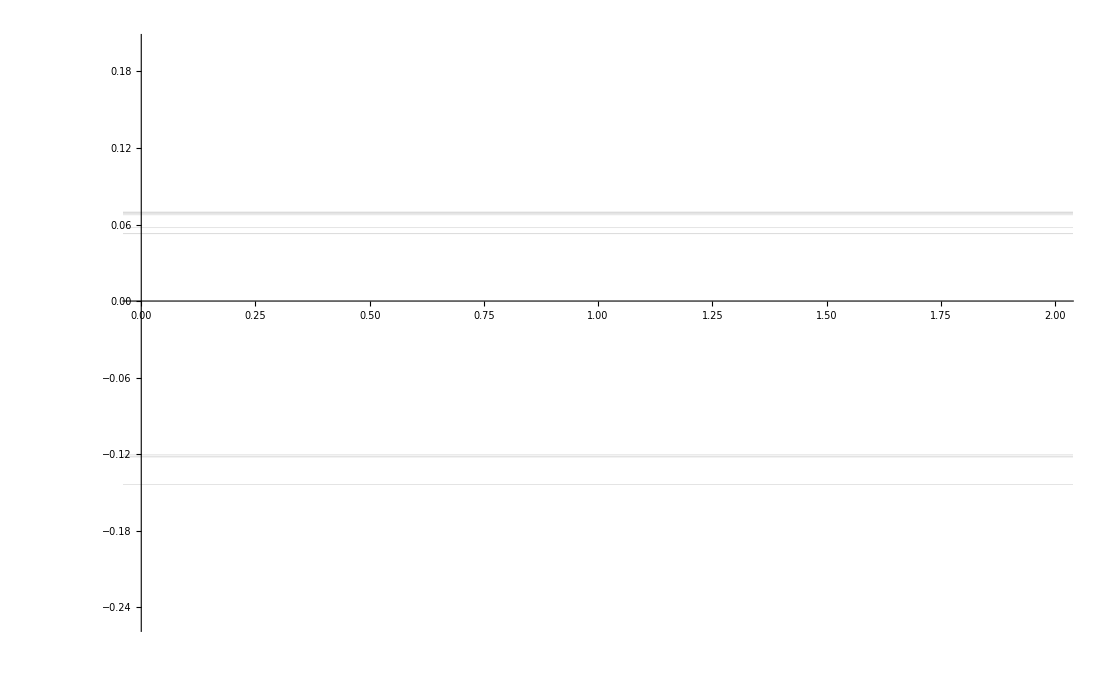

```mathematica
ListPlot[{1,2},PlotRange->{-.25,.2},GridLines->{{},Eigenvalues[fullhamiltonian/.{B->0,ℰ->0}]-2Brot},GridLinesStyle->Thick,AxesStyle->Large,Axes->{False,True}] (*This should match the figure from Hinds and Sandars 1980*)
```

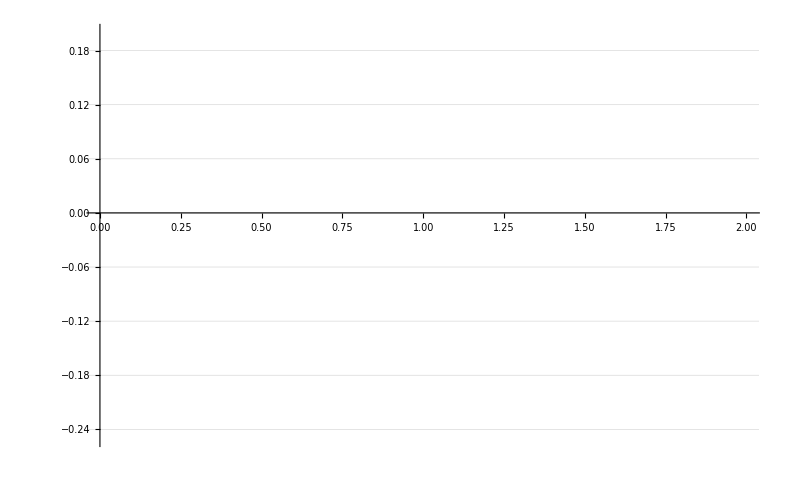

```mathematica
ListPlot[{1,2},PlotRange->{-.25,.2},GridLines->{{},Eigenvalues[fullhamiltonian/.{B->15,ℰ->40}]-2Brot},GridLinesStyle->Thick,AxesStyle->Large,Axes->{False,True}] (*This should match the figure from Hinds and Sandars 1980*)
```

```mathematica
Eigenvalues[fullhamiltonian/.{B->15,ℰ->40}]-2Brot
```

{66899.5,66899.5,66899.5,66899.5,66899.5,66899.5,66899.4,66899.4,66899.4,66899.4,66899.4,66899.4,66899.4,66899.4,66899.4,66899.4,66899.,66899.,66899.,66899.,66899.,66899.,66899.,66898.9,66898.9,66898.9,66898.9,66898.9,26759.9,26759.9,26759.9,26759.8,26759.8,26759.8,26759.8,26759.8,26759.8,26759.8,26759.8,26759.7,26759.5,26759.5,26759.5,26759.5,26759.5,26759.5,26759.5,26759.4,0.182877,0.157202,0.127116,0.095046,0.0639935,0.0134555,-0.00762709,-0.0343804,-0.114071,-0.123614,-0.15629,-0.203713,-13380.1,-13380.,-13380.,-13380.}

```mathematica
Round[Eigenvectors[fullhamiltonian/.B->100]ᵀ,.001]//MatrixForm
```

(0. | 0. | 0. | 0.001 | -0.001 | 0.002 | 0.001 | 0.003 | -0.043 | -0.997 | 0.064 | 0.027
0.001 | -0.007 | 0.041 | -0.99 | -0.108 | 0.049 | 0.039 | -0.039 | -0.022 | 0. | -0.006 | -0.004
0. | 0.005 | 0.008 | 0.034 | -0.052 | 0.065 | 0.007 | -0.035 | -0.927 | 0.016 | -0.362 | -0.017
-0.031 | 0.051 | -0.915 | 0.001 | -0.395 | -0.047 | -0.03 | 0.014 | 0.01 | 0. | 0.001 | -0.003
0. | 0.001 | 0.001 | 0.005 | -0.013 | 0.017 | 0.003 | -0.008 | -0.36 | 0.077 | 0.928 | 0.061
-0.008 | 0.012 | -0.397 | -0.1 | 0.894 | 0.146 | 0.09 | -0.051 | -0.042 | 0. | -0.006 | -0.001
0. | 0.005 | 0.008 | 0.049 | -0.059 | 0.116 | -0.034 | -0.957 | 0.044 | -0.01 | 0.023 | -0.247
-0.031 | -0.96 | -0.047 | 0.018 | -0.038 | 0.258 | -0.073 | 0.032 | 0.013 | 0. | 0.001 | 0.
0. | 0.001 | -0.001 | 0.007 | -0.013 | 0.019 | -0.031 | -0.245 | 0.018 | 0.02 | -0.061 | 0.966
0.017 | -0.273 | -0.024 | -0.038 | 0.1 | -0.907 | 0.265 | -0.131 | -0.062 | 0. | -0.007 | -0.004
0. | 0.003 | 0.01 | 0.063 | -0.125 | 0.258 | 0.955 | 0.004 | 0.034 | 0.001 | 0.002 | 0.024
0.999 | -0.024 | -0.032 | 0.002 | -0.007 | 0.023 | -0.007 | 0.003 | 0.001 | 0. | 0. | 0.)

```mathematica
Eigensystem[fullhamiltonian/.B->100]ᵀ//MatrixForm
```

(13380.2 | {-1.34141×10^-6,0.00116395,-0.000146265,-0.0306586,-0.0000164132,-0.00831141,-0.000169383,-0.0313621,-0.0000899407,0.016528,-0.000198298,0.998866}
13380.2 | {0.0000605006,-0.00743992,0.00469464,0.0512024,0.00061257,0.0124203,0.00535705,-0.960248,0.000727305,-0.272867,0.0032918,-0.0239486}
13380.1 | {0.000132335,0.040696,0.00791239,-0.914791,0.0012185,-0.396834,0.00797878,-0.0465144,-0.00149722,-0.0238738,0.0102513,-0.0324884}
13380. | {0.000655566,-0.990252,0.0340885,0.000890734,0.0049922,-0.100265,0.0485451,0.0177825,0.00716241,-0.0377783,0.0632873,0.00155691}
13379.9 | {-0.00121693,-0.108186,-0.0524889,-0.395202,-0.012758,0.893516,-0.0587167,-0.0379886,-0.0125401,0.100175,-0.125232,-0.00746337}
13379.8 | {0.00163773,0.049063,0.0648345,-0.046994,0.0172968,0.146072,0.116224,0.257958,0.0191311,-0.906702,0.257863,0.0229005}
13379.8 | {0.000747448,0.0388281,0.0072999,-0.0299029,0.00260373,0.0903181,-0.0340074,-0.0726293,-0.0309962,0.26452,0.954972,-0.00668674}
13379.8 | {0.00340367,-0.038975,-0.0349099,0.0136696,-0.00790879,-0.0505397,-0.957087,0.0319013,-0.2453,-0.131218,0.00382755,0.00302844}
13379.7 | {-0.042715,-0.0223735,-0.926823,0.0104635,-0.359568,-0.0422543,0.0444887,0.0134497,0.0177451,-0.0622312,0.0337621,0.00132182}
13379.6 | {-0.996647,-0.0000618252,0.0159952,-0.00015436,0.0769269,0.000302866,-0.0100488,-0.0000313449,0.0204658,0.000189385,0.000668649,-3.72423×10^-6}
13379.5 | {0.0643065,-0.00599498,-0.361908,0.00108788,0.927637,-0.0064214,0.0229877,0.00092569,-0.0609656,-0.00700827,0.00192415,0.0000930989}
13379.4 | {0.0267838,-0.00358098,-0.0169877,-0.00327288,0.061029,-0.000746353,-0.246606,0.000496417,0.966354,-0.00442719,0.0239042,0.0000348403})

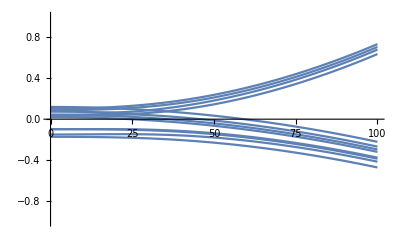

```mathematica
Plot[Eigenvalues[fullhamiltonian/.B->15]-2Brot,{ℰ,0,100},PlotRange->{-1,1}]
```